# Create Data

## Program

### R <-> MMA

```mathematica
makeClusterFromRdata[rdata_]:=Map[Drop[#,-1]&,Gather[Map[Drop[#,1]&,Drop[rdata,1]],#1[[-1]]==#2[[-1]]&],{2}]
```

```mathematica
makeClusterFromRdata[rdata_,"Nohead"]:=Map[Drop[#,-1]&,Gather[Map[Drop[#,1]&,rdata],#1[[-1]]==#2[[-1]]&],{2}]
```

```mathematica
makeClusterFromRdata[rdata_,"NoID"]:=Map[Drop[#,-1]&,Gather[Drop[rdata,1],#1[[-1]]==#2[[-1]]&],{2}]
```

```mathematica
makeClusterFromRdata[rdata_,op__]:=If[
Length[Flatten[Union[{{op},{"NoID","Nohead"}}]]]==2,
Map[Drop[#,-1]&,Gather[rdata,#1[[-1]]==#2[[-1]]&],{2}]
]
```

```mathematica
(*makeClusterFromRdata[rdata_,"NoID","Nohead"]:=Map[Drop[#,-1]&,Gather[rdata,#1[[-1]]==#2[[-1]]&],{2}]*)
```

```mathematica
makeRClusterFromMMAClData[cl_List]:=Module[
{len,dim,ClIDs},
len=Length[cl];
dim=Length[cl[[1,1]]];
ClIDs=Table[i,{i,len}];
Flatten[Table[Map[Append[#,i]&,cl[[i]]],{i,len}],1]
]
```

```mathematica
reginMax=1
```

1

```mathematica
regionMin=-1
```

-1

```mathematica
Get["/Users/amanokou/SCRIPT-MATHEMATICA/SCRIPTS/polar.txt"]
```

```mathematica
SetDirectory["/Users/amanokou/gitsrc/ClusteringAdequation/data"]
```

/Users/amanokou/gitsrc/ClusteringAdequation/data

```mathematica
createClusterdFileR[li_]:=Flatten[Table[Map[Append[#,n]&,li[[n]]],{n,Length[li]}],1]
```

```mathematica
testli2D={{{1,2},{1,2},{3,2}},{{3,3},{4,3}},{{4,4},{5,1},{1,4}},{{2,6},{4,6},{6,6},{7,1}}}
```

{{{1,2},{1,2},{3,2}},{{3,3},{4,3}},{{4,4},{5,1},{1,4}},{{2,6},{4,6},{6,6},{7,1}}}

```mathematica
createClusterdFileR[testli2D]
```

{{1,2,1},{1,2,1},{3,2,1},{3,3,2},{4,3,2},{4,4,3},{5,1,3},{1,4,3},{2,6,4},{4,6,4},{6,6,4},{7,1,4}}

## 2D, background, 200 - 1000; 200

```mathematica
bg[2][200]=Table[{RandomReal[{-1,1}],RandomReal[{-1,1}]},{200}];
```

```mathematica
bg[2][400]=Table[{RandomReal[{-1,1}],RandomReal[{-1,1}]},{400}];
```

```mathematica
bg[2][600]=Table[{RandomReal[{-1,1}],RandomReal[{-1,1}]},{600}];
```

```mathematica
bg[2][800]=Table[{RandomReal[{-1,1}],RandomReal[{-1,1}]},{800}];
```

```mathematica
bg[2][1000]=Table[{RandomReal[{-1,1}],RandomReal[{-1,1}]},{1000}];
```

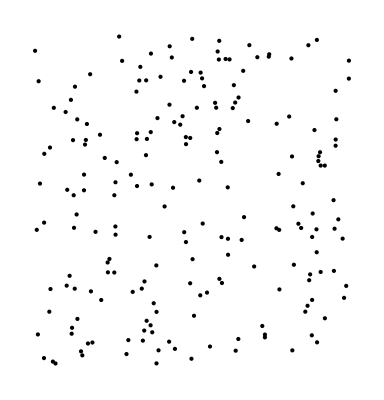

```mathematica
Graphics[Map[Point[#]&,bg[2][200]]]
```

```mathematica
(*Export["bg-2-200.tsv",bg[2][200]]*)
```

```mathematica
(*Export["bg-2-400.tsv",bg[2][400]]*)
```

```mathematica
(*Export["bg-2-600.tsv",bg[2][600]]*)
```

```mathematica
(*Export["bg-2-800.tsv",bg[2][800]]*)
```

```mathematica
(*Export["bg-2-1000.tsv",bg[2][1000]]*)
```

## 2D, normaldist;single, 2 - 20; 2

```mathematica
nd[2][2]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{2}];
```

```mathematica
For[i=2,i≤20,i+=2,Print[i];
nd[2][i]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{i}];
]
```

2

4

6

8

10

12

14

16

18

20

## 2D, normaldist;single, 200 - 1600; 200

```mathematica
nd[2][200]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{200}];
```

```mathematica
nd[2][400]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{400}];
```

```mathematica
nd2[2][400]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{400}];
```

```mathematica
nd[2][600]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{600}];
```

```mathematica
nd[2][800]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{800}];
```

```mathematica
nd[2][1000]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{1000}];
```

```mathematica
nd[2][1200]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{1200}];
```

```mathematica
nd[2][1400]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{1400}];
```

```mathematica
nd[2][1600]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{1600}];
```

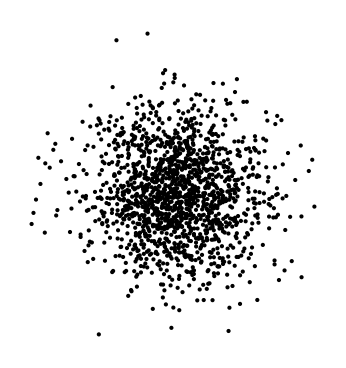

```mathematica
Graphics[Map[Point[#]&,nd[2][1600]]]
```

## 2D, 3Cls

```mathematica
correctdata[2][2][3]={Map[#+{0,0}&,nd[2][2]],Map[#+{5,0}&,nd[2][2]],Map[#+{2.5,3.5}&,nd[2][2]]}
```

{{{-0.688014,-0.0668755},{0.63496,-0.73258}},{{4.31199,-0.0668755},{5.63496,-0.73258}},{{1.81199,3.43312},{3.13496,2.76742}}}

```mathematica
makeRClusterFromMMAClData[correctdata[2][2][3]]
```

{{-0.688014,-0.0668755,1},{0.63496,-0.73258,1},{4.31199,-0.0668755,2},{5.63496,-0.73258,2},{1.81199,3.43312,3},{3.13496,2.76742,3}}

```mathematica
Directory[]
```

/Users/amanokou/gitsrc/ClusteringAdequation/data

```mathematica
(*Export["correctdata_2_2_3.tsv",correctdata[2][2][3]//makeRClusterFromMMAClData]*)
```

correctdata_2_2_3.tsv

```mathematica
correctdata[2][4][3]={Map[#+{0,0}&,nd[2][4]],Map[#+{5,0}&,nd[2][4]],Map[#+{2.5,3.5}&,nd[2][4]]}
```

{{{-0.498783,-0.713808},{-0.685304,0.741394},{0.884671,1.40825},{0.0999086,-0.0826385}},{{4.50122,-0.713808},{4.3147,0.741394},{5.88467,1.40825},{5.09991,-0.0826385}},{{2.00122,2.78619},{1.8147,4.24139},{3.38467,4.90825},{2.59991,3.41736}}}

```mathematica
(*Export["correctdata_2_4_3.tsv",correctdata[2][4][3]//makeRClusterFromMMAClData]*)
```

correctdata_2_4_3.tsv

```mathematica
correctdata[2][6][3]={Map[#+{0,0}&,nd[2][6]],Map[#+{5,0}&,nd[2][6]],Map[#+{2.5,3.5}&,nd[2][6]]}
```

{{{-0.122841,0.694022},{-1.40305,-0.687031},{0.454563,-0.971655},{-0.332609,2.01749},{1.14863,0.628713},{0.419892,0.128306}},{{4.87716,0.694022},{3.59695,-0.687031},{5.45456,-0.971655},{4.66739,2.01749},{6.14863,0.628713},{5.41989,0.128306}},{{2.37716,4.19402},{1.09695,2.81297},{2.95456,2.52834},{2.16739,5.51749},{3.64863,4.12871},{2.91989,3.62831}}}

```mathematica
(*Export["correctdata_2_6_3.tsv",correctdata[2][6][3]//makeRClusterFromMMAClData]*)
```

correctdata_2_6_3.tsv

## 2D, orverlapped

```mathematica
ndOv[2,1]=Join[Map[#+{1,3.6}&,nd[2][400]],Map[#&,nd2[2][400]],Map[#+{10,2}&,nd[2][400]]];
```

```mathematica
Dimensions[ndOv[2,1]]
```

{1200,2}

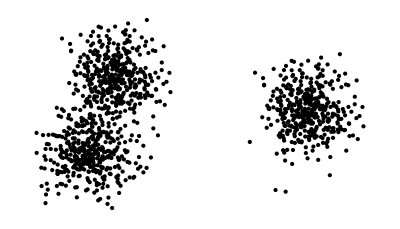

```mathematica
Graphics[Map[Point[#]&,ndOv[2,1]]]
```

```mathematica
(*Export["overlapped2D.tsv",ndOv[2,1]]*)
```

overlapped2D.tsv

## 2D, unbalanced

```mathematica
ndUb[3]=Join[Map[#+{1,6}&,nd[2][400]],Map[#*0.5&,nd2[2][400]],Map[#+{10,2}&,nd2[2][400]]];
```

```mathematica
Dimensions[ndUb[3]]
```

{1200,2}

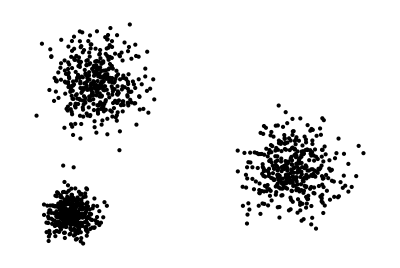

```mathematica
Graphics[Map[Point[#]&,ndUb[3]]]
```

```mathematica
(*Export["unbalanced2D.tsv",ndUb[3]]*)
```

unbalanced2D.tsv

```mathematica
(*Export["unbalanced2D_x10.tsv",ndUb[3]*10]*)
```

unbalanced2D_x10.tsv

```mathematica
(*Export["unbalanced2D_x10E-1.tsv",ndUb[3]/10]*)
```

unbalanced2D_x10E-1.tsv

## 2D, subcluster

```mathematica
ndSubs[5]=Join[Map[#+{0,0}&,nd[2][400]],Map[#*1.1+{0,6}&,nd2[2][400]],Map[#*1.2+{18,0}&,nd2[2][400]],Map[#+{17,6}&,nd[2][400]],Map[#*1.4+{7,17}&,nd2[2][400]]];
```

```mathematica
Dimensions[ndSubs[5]]
```

{2000,2}

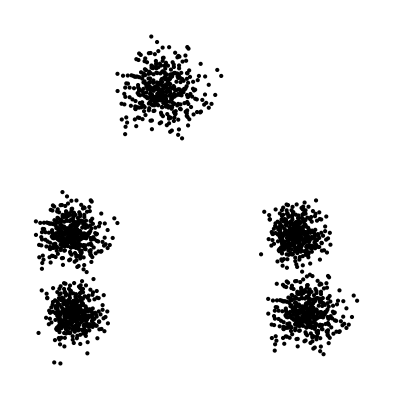

```mathematica
Graphics[Map[Point[#]&,ndSubs[5]]]
```

```mathematica
(*Export["subcluster2D.tsv",ndSubs[5]]*)
```

subcluster2D.tsv

## 2D, noisy

```mathematica
shifts={{6.8,2.5},{4.5,6.1},{4.0,3.2},{2.0,1.7},{8.5,4.8},{2.0,5.4},{5.9,0.3}}
```

{{6.8,2.5},{4.5,6.1},{4.,3.2},{2.,1.7},{8.5,4.8},{2.,5.4},{5.9,0.3}}

```mathematica
scales={0.25,0.3,0.18,0.3,0.28,0.3,0.3}
```

{0.25,0.3,0.18,0.3,0.28,0.3,0.3}

```mathematica
(nd[7,"correct"]=Table[Map[#*scales[[n]]+shifts[[n]]&,nd[2][200]],{n,Length[shifts]}])//Length
```

7

```mathematica
nd[7,"correct","centroids"]=Map[Mean[#]&,nd[7,"correct"]]
```

{{6.78756,2.46707},{4.48507,6.06048},{3.99104,3.17629},{1.98507,1.66048},{8.48607,4.76312},{1.98507,5.36048},{5.88507,0.260483}}

```mathematica
nd[7,"correct","1/10","centroids"]=Map[Mean[#]&,nd[7,"correct"]/10]
```

{{0.678756,0.246707},{0.448507,0.606048},{0.399104,0.317629},{0.198507,0.166048},{0.848607,0.476312},{0.198507,0.536048},{0.588507,0.0260483}}

```mathematica
(nd[7]=Flatten[Table[Map[#*scales[[n]]+shifts[[n]]&,nd[2][200]],{n,Length[shifts]}],1])//Dimensions
```

{1400,2}

```mathematica
(nd[7,"correct","R"]=createClusterdFileR[nd[7,"correct"]])//Length
```

1400

```mathematica
(nd[7,"correct","R","1/10"]=createClusterdFileR[nd[7,"correct"]/10])//Length
```

1400

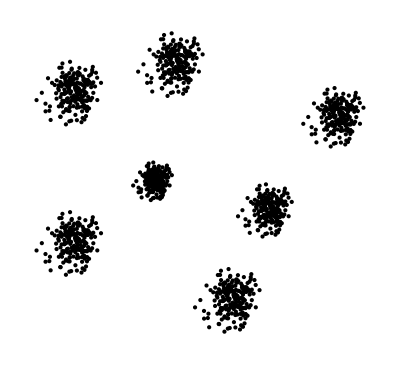

```mathematica
Graphics[Map[Point[#]&,nd[7]],PlotRange->All]
```

```mathematica
(*Export["nd7.tsv",nd[7]]*)
```

```mathematica
(*Export["nd7_x10E-1.tsv",nd[7]/10]*)
```

```mathematica
nd[7,"correct","R"]//Length
```

1400

```mathematica
(*Export["nd7_correct_R.tsv",nd[7,"correct","R"]]*)
```

```mathematica
(*Export["nd7_correct_R.cent.tsv",nd[7,"correct","centroids"]]*)
```

```mathematica
(*Export["nd7_correct_R_x10E-1.tsv",nd[7,"correct","R","1/10"]]*)
```

```mathematica
(*Export["nd7_correct_R_x10E-1.cent.tsv",nd[7,"correct","1/10","centroids"]]*)
```

```mathematica
FindClusters[nd[7],Method->"Agglomerate"]//Length
```

1

```mathematica
nois=Map[#+{5,3.2}&,bg[2][400]*5.4];
```

```mathematica
noisy[7]=Join[nd[7],nois];
```

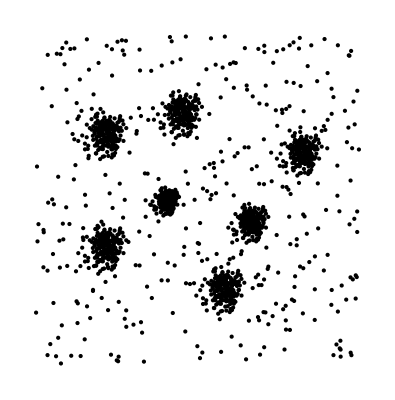

```mathematica
Graphics[Map[Point[#]&,noisy[7]]]
```

```mathematica
(*Export["noisy7.tsv",noisy[7]]*)
```

noisy7.tsv

```mathematica
(*Export["noisy7_x10E-1.tsv",noisy[7]/10]*)
```

noisy7_x10E-1.tsv

```mathematica
FindClusters[noisy[7],7,Method->"Optimize"]//Length
```

7

```mathematica
FindClusters[noisy[7],Method->"Agglomerate"]//Length
```

1

```mathematica
FindClusters[noisy[7],Method->"Optimize"]//Length
```

2

## 2D, 60 samples, 6 clusters, each cluster has 10 samples.

わかりやすいデータ、6クラスタ、60サンプル、各クラスタに10メンバー、2次元

```mathematica
rt6=Map[polarToxy[{1,#}]&,Table[2 Pi n/6,{n,1,6}]]
```

{{1/2,(√3)/2},{-1/2,(√3)/2},{-1,0},{-1/2,-(√3)/2},{1/2,-(√3)/2},{1,0}}

```mathematica
Graphics[Map[Point[#]&,rt6]]
```

-Graphics-

```mathematica
dataCLrt6=Transpose[Table[rt6,{10}]]
```

{{{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2}},{{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2}},{{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0}},{{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2}},{{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2}},{{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}}}

```mathematica
dataFLrt6=Flatten[dataCLrt6,1]
```

{{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}}

```mathematica
(*Export["dataFLrt6.tsv",dataFLrt6]*)
```

dataFLrt6.tsv

## 2D, 50 samples, 10 clusters

```mathematica
rt10=Map[polarToxy[{1,#}]&,Table[2 Pi n/10,{n,1,10}]]//N
```

{{0.809017,0.587785},{0.309017,0.951057},{-0.309017,0.951057},{-0.809017,0.587785},{-1.,0.},{-0.809017,-0.587785},{-0.309017,-0.951057},{0.309017,-0.951057},{0.809017,-0.587785},{1.,0.}}

```mathematica
rt10table5=Transpose[Table[rt10,{5}]];
```

```mathematica
rt10table5R=makeRClusterFromMMAClData[rt10table5]
```

{{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10}}

```mathematica
(*Export["rt10table5R.tsv",rt10table5R]*)
```

rt10table5R.tsv

```mathematica
Directory[]
```

/Users/amanokou/TEST_COLLECTION/ClusteringAdequation/data

## 2D, 100 samples, 10 clusters

```mathematica
rt10=Map[polarToxy[{1,#}]&,Table[2 Pi n/10,{n,1,10}]]//N
```

{{0.809017,0.587785},{0.309017,0.951057},{-0.309017,0.951057},{-0.809017,0.587785},{-1.,0.},{-0.809017,-0.587785},{-0.309017,-0.951057},{0.309017,-0.951057},{0.809017,-0.587785},{1.,0.}}

```mathematica
rt10table10=Transpose[Table[rt10,{10}]];
```

```mathematica
rt10table10R=makeRClusterFromMMAClData[rt10table10]
```

{{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10}}

```mathematica
(*Export["rt10table10R.tsv",rt10table10R]*)
```

rt10table10R.tsv

```mathematica
Directory[]
```

/Users/amanokou/TEST_COLLECTION/ClusteringAdequation/data

## 10D, 100 samples, 10 clusters

```mathematica
id10=IdentityMatrix[10];
```

```mathematica
id10Table10=Transpose[Table[id10,{10}]];
```

```mathematica
id10Table10R=makeRClusterFromMMAClData[id10Table10]
```

{{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10}}

## 10D, 50 samples, 10 clusters

```mathematica
id10=IdentityMatrix[10];
```

```mathematica
id10Table5=Transpose[Table[id10,{5}]];
```

```mathematica
id10Table5R=makeRClusterFromMMAClData[id10Table5]
```

{{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10}}

## TEST

```mathematica
SetDirectory["/Users/amanokou/gitsrc/ClusteringAdequation/data"]
```

/Users/amanokou/gitsrc/ClusteringAdequation/data

```mathematica
Directory[]
```

/Users/amanokou/gitsrc/ClusteringAdequation/data

```mathematica
Import["nd7_correct_R.tsv"]
```

{{6.92177,2.60617,1},{6.93236,2.44081,1},{7.12737,2.50477,1},{6.78266,2.46778,1},{6.83519,2.46326,1},{6.746,2.75492,1},{6.66431,2.6248,1},{6.76204,1.90206,1},{6.32128,2.12198,1},{6.47039,2.43628,1},{6.77625,2.67073,1},{6.87018,2.37356,1},{6.73239,2.80611,1},{6.95357,2.27699,1},{6.32785,2.61299,1},{6.74273,2.80558,1},{6.68974,2.46677,1},{7.09868,2.28573,1},{6.88551,2.1528,1},{6.68412,2.74542,1},{6.85122,2.51733,1},{6.4579,2.38726,1},{6.83285,2.3682,1},{7.09299,2.24333,1},{6.78485,2.61421,1},{6.49734,2.72036,1},{6.62393,2.4579,1},{6.3842,2.15035,1},{7.30161,2.14737,1},{6.60559,2.31919,1},{6.94978,2.54629,1},{6.30766,2.88234,1},{6.86954,2.4015,1},{6.93503,2.5343,1},{6.61921,2.49554,1},{7.0977,2.38854,1},{6.71254,2.41322,1},{6.96551,2.44923,1},{6.91022,2.4561,1},{6.64316,2.75645,1},{6.81659,2.70005,1},{6.78911,2.31654,1},{6.76146,2.49807,1},{6.70883,2.65185,1},{6.94116,2.34584,1},{6.69362,2.55843,1},{7.54689,1.80223,1},{6.7595,2.47636,1},{7.00272,2.06797,1},{6.70609,2.5917,1},{6.60804,2.4551,1},{6.46747,2.6304,1},{6.37129,2.29416,1},{6.5536,2.43646,1},{7.02304,2.88162,1},{6.71266,2.63646,1},{6.83579,2.63399,1},{6.73513,2.1444,1},{6.85493,2.52132,1},{6.803,2.86697,1},{6.87508,2.16734,1},{6.769,2.36777,1},{6.71351,1.9609,1},{6.5419,2.64039,1},{6.54381,2.49924,1},{6.48028,2.24191,1},{6.66508,2.13183,1},{6.80832,2.55793,1},{7.06991,2.42132,1},{7.10274,2.22619,1},{6.32626,2.31485,1},{7.11127,2.49415,1},{7.19453,2.97507,1},{6.87562,2.30031,1},{6.80333,2.2947,1},{6.83298,2.73481,1},{6.45016,2.76289,1},{6.69755,2.36054,1},{6.45071,2.53568,1},{6.91442,2.4419,1},{6.87,2.77038,1},{6.59473,2.92613,1},{5.83749,2.38824,1},{6.45114,3.11008,1},{7.48558,2.31198,1},{6.63475,2.33148,1},{6.99117,3.00096,1},{6.27617,2.18737,1},{7.08057,2.53402,1},{6.83891,2.31054,1},{6.50687,2.33672,1},{6.52106,2.48156,1},{6.7396,2.56236,1},{6.98168,2.42948,1},{6.78042,2.70946,1},{6.86985,2.22163,1},{7.2013,2.58071,1},{6.55427,3.00311,1},{6.10281,2.23216,1},{6.71888,2.49855,1},{6.93126,3.03476,1},{7.06414,2.86161,1},{6.62911,2.02186,1},{6.51357,2.49425,1},{6.24907,3.13671,1},{7.35967,2.30544,1},{6.60827,2.32855,1},{6.52515,2.2234,1},{6.82432,2.30065,1},{7.10022,3.02979,1},{6.78093,2.28599,1},{6.98409,2.22702,1},{6.97215,2.46846,1},{6.8372,2.18084,1},{7.14407,2.10741,1},{6.53861,2.28235,1},{6.52242,2.80239,1},{6.93716,2.49053,1},{6.90623,2.31356,1},{6.97237,2.83011,1},{6.06134,2.33926,1},{6.95953,2.65377,1},{6.52274,2.48556,1},{6.62587,2.27395,1},{6.83869,2.11711,1},{6.83782,2.80489,1},{6.17963,2.20705,1},{6.78483,2.46584,1},{6.95671,3.12534,1},{6.38648,2.40809,1},{6.80484,2.46012,1},{6.82059,2.80325,1},{6.43723,2.35524,1},{6.59538,2.3921,1},{6.44457,2.51729,1},{6.87951,2.52358,1},{7.15914,2.50197,1},{6.51153,2.35659,1},{6.7921,2.28181,1},{7.25394,2.61435,1},{6.29645,2.66991,1},{7.21612,2.96977,1},{6.28175,2.1289,1},{6.75683,2.14944,1},{6.44605,2.65056,1},{6.95339,2.40091,1},{6.90134,2.86817,1},{6.84023,2.71864,1},{6.75172,2.4323,1},{7.12918,2.56683,1},{6.84744,2.31627,1},{6.65342,2.59804,1},{6.52109,2.64068,1},{6.71358,2.78035,1},{7.06006,2.566,1},{6.54422,1.94558,1},{6.74345,2.43648,1},{6.42722,2.56519,1},{6.94874,2.78831,1},{7.32148,2.75867,1},{6.77147,2.43696,1},{7.34846,2.1544,1},{6.98097,2.19838,1},{6.98968,2.50561,1},{6.78486,2.51842,1},{6.61975,2.58567,1},{6.92497,2.37598,1},{6.80031,2.64859,1},{6.88464,2.38725,1},{7.01335,2.63281,1},{6.88387,2.32629,1},{6.75909,2.44223,1},{6.90789,2.56469,1},{7.14786,2.69001,1},{7.18449,2.81453,1},{6.59479,2.54515,1},{6.56239,1.9846,1},{7.06686,2.50816,1},{6.62162,2.40925,1},{6.35907,2.25224,1},{6.65591,2.75142,1},{6.7845,2.49515,1},{6.7885,2.53335,1},{6.74244,2.58709,1},{6.85976,2.42912,1},{7.17542,2.82382,1},{6.85826,2.41857,1},{6.54125,2.24354,1},{6.95344,2.43446,1},{6.72754,2.32844,1},{6.79989,2.40238,1},{6.75031,2.08392,1},{6.47734,2.56588,1},{6.56573,2.70517,1},{6.61622,2.48333,1},{6.76092,2.23243,1},{7.12727,2.8039,1},{6.78627,2.46538,1},{7.04261,2.59414,1},{7.30517,2.63122,1},{4.64612,6.22741,2},{4.65883,6.02897,2},{4.89284,6.10572,2},{4.47919,6.06134,2},{4.54222,6.05592,2},{4.4352,6.4059,2},{4.33717,6.24976,2},{4.45445,5.38247,2},{3.92554,5.64638,2},{4.10447,6.02354,2},{4.4715,6.30488,2},{4.58422,5.94827,2},{4.41887,6.46733,2},{4.68428,5.83239,2},{3.93342,6.23559,2},{4.43128,6.46669,2},{4.36769,6.06012,2},{4.85842,5.84288,2},{4.60261,5.68336,2},{4.36095,6.39451,2},{4.56146,6.1208,2},{4.08949,5.96471,2},{4.53942,5.94185,2},{4.85159,5.79199,2},{4.48182,6.23705,2},{4.13681,6.36443,2},{4.28871,6.04948,2},{4.00105,5.68042,2},{5.10193,5.67684,2},{4.26671,5.88303,2},{4.67974,6.15555,2},{3.90919,6.55881,2},{4.58345,5.9818,2},{4.66204,6.14117,2},{4.28305,6.09465,2},{4.85724,5.96625,2},{4.39504,5.99587,2},{4.69861,6.03908,2},{4.63227,6.04732,2},{4.3118,6.40773,2},{4.51991,6.34006,2},{4.48694,5.87985,2},{4.45375,6.09769,2},{4.39059,6.28222,2},{4.66939,5.915,2},{4.37235,6.17011,2},{5.39626,5.26267,2},{4.4514,6.07163,2},{4.74327,5.58156,2},{4.38731,6.21003,2},{4.26964,6.04612,2},{4.10097,6.25648,2},{3.98555,5.85299,2},{4.20432,6.02376,2},{4.76764,6.55794,2},{4.39519,6.26376,2},{4.54295,6.26078,2},{4.42216,5.67328,2},{4.56591,6.12559,2},{4.50361,6.54036,2},{4.5901,5.70081,2},{4.4628,5.94132,2},{4.39622,5.45308,2},{4.19028,6.26847,2},{4.19257,6.09908,2},{4.11634,5.79029,2},{4.3381,5.6582,2},{4.50999,6.16951,2},{4.8239,6.00558,2},{4.86329,5.77142,2},{3.93151,5.87782,2},{4.87352,6.09298,2},{4.97343,6.67008,2},{4.59074,5.86038,2},{4.504,5.85364,2},{4.53958,6.38177,2},{4.08019,6.41547,2},{4.37706,5.93265,2},{4.08085,6.14281,2},{4.6373,6.03028,2},{4.584,6.42446,2},{4.25368,6.61135,2},{3.34499,5.96589,2},{4.08136,6.8321,2},{5.32269,5.87438,2},{4.3017,5.89777,2},{4.7294,6.70115,2},{3.87141,5.72484,2},{4.83669,6.14082,2},{4.54669,5.87265,2},{4.14824,5.90406,2},{4.16527,6.07787,2},{4.42752,6.17484,2},{4.71801,6.01537,2},{4.4765,6.35135,2},{4.58382,5.76595,2},{4.98156,6.19685,2},{4.20512,6.70373,2},{3.66337,5.77859,2},{4.40266,6.09826,2},{4.65752,6.74171,2},{4.81696,6.53394,2},{4.29493,5.52623,2},{4.15629,6.0931,2},{3.83888,6.86405,2},{5.17161,5.86653,2},{4.26992,5.89426,2},{4.17018,5.76808,2},{4.52919,5.86078,2},{4.86027,6.73575,2},{4.47711,5.84319,2},{4.72091,5.77243,2},{4.70658,6.06215,2},{4.54465,5.717,2},{4.91289,5.62889,2},{4.18633,5.83882,2},{4.1669,6.46287,2},{4.66459,6.08863,2},{4.62748,5.87627,2},{4.70684,6.49613,2},{3.61361,5.90711,2},{4.69144,6.28452,2},{4.16729,6.08268,2},{4.29104,5.82874,2},{4.54643,5.64053,2},{4.54538,6.46586,2},{3.75556,5.74847,2},{4.4818,6.059,2},{4.68805,6.85041,2},{4.00377,5.98971,2},{4.5058,6.05215,2},{4.52471,6.4639,2},{4.06468,5.92628,2},{4.25445,5.97053,2},{4.07348,6.12074,2},{4.59541,6.12829,2},{4.93097,6.10236,2},{4.15384,5.9279,2},{4.49052,5.83817,2},{5.04473,6.23722,2},{3.89574,6.30389,2},{4.99935,6.66373,2},{3.8781,5.65468,2},{4.44819,5.67932,2},{4.07526,6.28067,2},{4.68407,5.9811,2},{4.62161,6.54181,2},{4.54828,6.36237,2},{4.44207,6.01876,2},{4.89501,6.1802,2},{4.55693,5.87953,2},{4.3241,6.21765,2},{4.16531,6.26882,2},{4.3963,6.43641,2},{4.81208,6.1792,2},{4.19306,5.4347,2},{4.43213,6.02377,2},{4.05267,6.17823,2},{4.67848,6.44597,2},{5.12578,6.41041,2},{4.46576,6.02435,2},{5.15815,5.68528,2},{4.71716,5.73805,2},{4.72762,6.10674,2},{4.48183,6.12211,2},{4.2837,6.2028,2},{4.64997,5.95118,2},{4.50037,6.27831,2},{4.60157,5.9647,2},{4.75602,6.25937,2},{4.60065,5.89155,2},{4.45091,6.03068,2},{4.62947,6.17763,2},{4.91743,6.32801,2},{4.96139,6.47744,2},{4.25374,6.15418,2},{4.21486,5.48152,2},{4.82023,6.10979,2},{4.28594,5.9911,2},{3.97088,5.80269,2},{4.3271,6.4017,2},{4.4814,6.09418,2},{4.4862,6.14002,2},{4.43093,6.20451,2},{4.57171,6.01494,2},{4.9505,6.48859,2},{4.56992,6.00229,2},{4.1895,5.79225,2},{4.68413,6.02135,2},{4.41305,5.89413,2},{4.49986,5.98286,2},{4.44038,5.6007,2},{4.1128,6.17905,2},{4.21887,6.34621,2},{4.27947,6.07999,2},{4.45311,5.77892,2},{4.89272,6.46468,2},{4.48352,6.05846,2},{4.79114,6.21297,2},{5.1062,6.25747,2},{4.08767,3.27644,3},{4.0953,3.15738,3},{4.23571,3.20343,3},{3.98752,3.1768,3},{4.02533,3.17355,3},{3.96112,3.38354,3},{3.9023,3.28986,3},{3.97267,2.76948,3},{3.65532,2.92783,3},{3.76268,3.15412,3},{3.9829,3.32293,3},{4.05053,3.10896,3},{3.95132,3.4204,3},{4.11057,3.03943,3},{3.66005,3.28135,3},{3.95877,3.42001,3},{3.92062,3.17607,3},{4.21505,3.04573,3},{4.06156,2.95002,3},{3.91657,3.37671,3},{4.03688,3.21248,3},{3.75369,3.11883,3},{4.02365,3.10511,3},{4.21096,3.0152,3},{3.98909,3.28223,3},{3.78208,3.35866,3},{3.87323,3.16969,3},{3.70063,2.94825,3},{4.36116,2.9461,3},{3.86003,3.06982,3},{4.10784,3.23333,3},{3.64551,3.47529,3},{4.05007,3.12908,3},{4.09722,3.2247,3},{3.86983,3.19679,3},{4.21435,3.11975,3},{3.93703,3.13752,3},{4.11917,3.16345,3},{4.07936,3.16839,3},{3.88708,3.38464,3},{4.01195,3.34403,3},{3.99216,3.06791,3},{3.97225,3.19861,3},{3.93436,3.30933,3},{4.10164,3.089,3},{3.92341,3.24207,3},{4.53776,2.6976,3},{3.97084,3.18298,3},{4.14596,2.88894,3},{3.93238,3.26602,3},{3.86179,3.16767,3},{3.76058,3.29389,3},{3.69133,3.0518,3},{3.82259,3.15425,3},{4.16059,3.47476,3},{3.93711,3.29825,3},{4.02577,3.29647,3},{3.95329,2.94397,3},{4.03955,3.21535,3},{4.00216,3.46422,3},{4.05406,2.96048,3},{3.97768,3.10479,3},{3.93773,2.81185,3},{3.81417,3.30108,3},{3.81554,3.19945,3},{3.7698,3.01418,3},{3.90286,2.93492,3},{4.00599,3.24171,3},{4.19434,3.14335,3},{4.21797,3.00285,3},{3.65891,3.06669,3},{4.22411,3.19579,3},{4.28406,3.54205,3},{4.05445,3.05623,3},{4.0024,3.05218,3},{4.02375,3.36906,3},{3.74811,3.38928,3},{3.92623,3.09959,3},{3.74851,3.22569,3},{4.08238,3.15817,3},{4.0504,3.39468,3},{3.85221,3.50681,3},{3.307,3.11953,3},{3.74882,3.63926,3},{4.49362,3.06463,3},{3.88102,3.07866,3},{4.13764,3.56069,3},{3.62284,2.9749,3},{4.20201,3.22449,3},{4.02802,3.06359,3},{3.78894,3.08244,3},{3.79916,3.18672,3},{3.95651,3.2449,3},{4.13081,3.14922,3},{3.9859,3.35081,3},{4.05029,2.99957,3},{4.28894,3.25811,3},{3.82307,3.56224,3},{3.49802,3.00715,3},{3.9416,3.19895,3},{4.09451,3.58503,3},{4.19018,3.46036,3},{3.87696,2.85574,3},{3.79377,3.19586,3},{3.60333,3.65843,3},{4.40296,3.05992,3},{3.86195,3.07656,3},{3.80211,3.00085,3},{4.01751,3.05647,3},{4.21616,3.58145,3},{3.98627,3.04591,3},{4.13254,3.00346,3},{4.12395,3.17729,3},{4.02679,2.9702,3},{4.24773,2.91733,3},{3.8118,3.04329,3},{3.80014,3.41772,3},{4.09876,3.19318,3},{4.07649,3.06576,3},{4.1241,3.43768,3},{3.46817,3.08427,3},{4.11486,3.31071,3},{3.80037,3.18961,3},{3.87462,3.03724,3},{4.02786,2.92432,3},{4.02723,3.41952,3},{3.55334,2.98908,3},{3.98908,3.1754,3},{4.11283,3.65025,3},{3.70226,3.13383,3},{4.00348,3.17129,3},{4.01482,3.41834,3},{3.73881,3.09577,3},{3.85267,3.12232,3},{3.74409,3.21245,3},{4.05725,3.21698,3},{4.25858,3.20142,3},{3.7923,3.09674,3},{3.99431,3.0429,3},{4.32684,3.28233,3},{3.63744,3.32234,3},{4.29961,3.53824,3},{3.62686,2.93281,3},{3.96891,2.94759,3},{3.74515,3.3084,3},{4.11044,3.12866,3},{4.07297,3.46509,3},{4.02897,3.35742,3},{3.96524,3.15126,3},{4.23701,3.24812,3},{4.03416,3.06772,3},{3.89446,3.27059,3},{3.79918,3.30129,3},{3.93778,3.40185,3},{4.18725,3.24752,3},{3.81584,2.80082,3},{3.95928,3.15426,3},{3.7316,3.24694,3},{4.10709,3.40758,3},{4.37547,3.38625,3},{3.97946,3.15461,3},{4.39489,2.95117,3},{4.1303,2.98283,3},{4.13657,3.20404,3},{3.9891,3.21326,3},{3.87022,3.26168,3},{4.08998,3.11071,3},{4.00022,3.30699,3},{4.06094,3.11882,3},{4.15361,3.29562,3},{4.06039,3.07493,3},{3.97054,3.15841,3},{4.07768,3.24658,3},{4.25046,3.33681,3},{4.27683,3.42646,3},{3.85225,3.23251,3},{3.82892,2.82891,3},{4.19214,3.20587,3},{3.87156,3.13466,3},{3.68253,3.02161,3},{3.89626,3.38102,3},{3.98884,3.19651,3},{3.99172,3.22401,3},{3.95856,3.26271,3},{4.04303,3.14897,3},{4.2703,3.43315,3},{4.04195,3.14137,3},{3.8137,3.01535,3},{4.11048,3.15281,3},{3.94783,3.07648,3},{3.99992,3.12971,3},{3.96423,2.90042,3},{3.76768,3.24743,3},{3.83132,3.34772,3},{3.86768,3.18799,3},{3.97187,3.00735,3},{4.23563,3.41881,3},{3.99011,3.17507,3},{4.17468,3.26778,3},{4.36372,3.29448,3},{2.14612,1.82741,4},{2.15883,1.62897,4},{2.39284,1.70572,4},{1.97919,1.66134,4},{2.04222,1.65592,4},{1.9352,2.0059,4},{1.83717,1.84976,4},{1.95445,0.982473,4},{1.42554,1.24638,4},{1.60447,1.62354,4},{1.9715,1.90488,4},{2.08422,1.54827,4},{1.91887,2.06733,4},{2.18428,1.43239,4},{1.43342,1.83559,4},{1.93128,2.06669,4},{1.86769,1.66012,4},{2.35842,1.44288,4},{2.10261,1.28336,4},{1.86095,1.99451,4},{2.06146,1.7208,4},{1.58949,1.56471,4},{2.03942,1.54185,4},{2.35159,1.39199,4},{1.98182,1.83705,4},{1.63681,1.96443,4},{1.78871,1.64948,4},{1.50105,1.28042,4},{2.60193,1.27684,4},{1.76671,1.48303,4},{2.17974,1.75555,4},{1.40919,2.15881,4},{2.08345,1.5818,4},{2.16204,1.74117,4},{1.78305,1.69465,4},{2.35724,1.56625,4},{1.89504,1.59587,4},{2.19861,1.63908,4},{2.13227,1.64732,4},{1.8118,2.00773,4},{2.01991,1.94006,4},{1.98694,1.47985,4},{1.95375,1.69769,4},{1.89059,1.88222,4},{2.16939,1.515,4},{1.87235,1.77011,4},{2.89626,0.862671,4},{1.9514,1.67163,4},{2.24327,1.18156,4},{1.88731,1.81003,4},{1.76964,1.64612,4},{1.60097,1.85648,4},{1.48555,1.45299,4},{1.70432,1.62376,4},{2.26764,2.15794,4},{1.89519,1.86376,4},{2.04295,1.86078,4},{1.92216,1.27328,4},{2.06591,1.72559,4},{2.00361,2.14036,4},{2.0901,1.30081,4},{1.9628,1.54132,4},{1.89622,1.05308,4},{1.69028,1.86847,4},{1.69257,1.69908,4},{1.61634,1.39029,4},{1.8381,1.2582,4},{2.00999,1.76951,4},{2.3239,1.60558,4},{2.36329,1.37142,4},{1.43151,1.47782,4},{2.37352,1.69298,4},{2.47343,2.27008,4},{2.09074,1.46038,4},{2.004,1.45364,4},{2.03958,1.98177,4},{1.58019,2.01547,4},{1.87706,1.53265,4},{1.58085,1.74281,4},{2.1373,1.63028,4},{2.084,2.02446,4},{1.75368,2.21135,4},{0.844993,1.56589,4},{1.58136,2.4321,4},{2.82269,1.47438,4},{1.8017,1.49777,4},{2.2294,2.30115,4},{1.37141,1.32484,4},{2.33669,1.74082,4},{2.04669,1.47265,4},{1.64824,1.50406,4},{1.66527,1.67787,4},{1.92752,1.77484,4},{2.21801,1.61537,4},{1.9765,1.95135,4},{2.08382,1.36595,4},{2.48156,1.79685,4},{1.70512,2.30373,4},{1.16337,1.37859,4},{1.90266,1.69826,4},{2.15752,2.34171,4},{2.31696,2.13394,4},{1.79493,1.12623,4},{1.65629,1.6931,4},{1.33888,2.46405,4},{2.67161,1.46653,4},{1.76992,1.49426,4},{1.67018,1.36808,4},{2.02919,1.46078,4},{2.36027,2.33575,4},{1.97711,1.44319,4},{2.22091,1.37243,4},{2.20658,1.66215,4},{2.04465,1.317,4},{2.41289,1.22889,4},{1.68633,1.43882,4},{1.6669,2.06287,4},{2.16459,1.68863,4},{2.12748,1.47627,4},{2.20684,2.09613,4},{1.11361,1.50711,4},{2.19144,1.88452,4},{1.66729,1.68268,4},{1.79104,1.42874,4},{2.04643,1.24053,4},{2.04538,2.06586,4},{1.25556,1.34847,4},{1.9818,1.659,4},{2.18805,2.45041,4},{1.50377,1.58971,4},{2.0058,1.65215,4},{2.02471,2.0639,4},{1.56468,1.52628,4},{1.75445,1.57053,4},{1.57348,1.72074,4},{2.09541,1.72829,4},{2.43097,1.70236,4},{1.65384,1.5279,4},{1.99052,1.43817,4},{2.54473,1.83722,4},{1.39574,1.90389,4},{2.49935,2.26373,4},{1.3781,1.25468,4},{1.94819,1.27932,4},{1.57526,1.88067,4},{2.18407,1.5811,4},{2.12161,2.14181,4},{2.04828,1.96237,4},{1.94207,1.61876,4},{2.39501,1.7802,4},{2.05693,1.47953,4},{1.8241,1.81765,4},{1.66531,1.86882,4},{1.8963,2.03641,4},{2.31208,1.7792,4},{1.69306,1.0347,4},{1.93213,1.62377,4},{1.55267,1.77823,4},{2.17848,2.04597,4},{2.62578,2.01041,4},{1.96576,1.62435,4},{2.65815,1.28528,4},{2.21716,1.33805,4},{2.22762,1.70674,4},{1.98183,1.72211,4},{1.7837,1.8028,4},{2.14997,1.55118,4},{2.00037,1.87831,4},{2.10157,1.5647,4},{2.25602,1.85937,4},{2.10065,1.49155,4},{1.95091,1.63068,4},{2.12947,1.77763,4},{2.41743,1.92801,4},{2.46139,2.07744,4},{1.75374,1.75418,4},{1.71486,1.08152,4},{2.32023,1.70979,4},{1.78594,1.5911,4},{1.47088,1.40269,4},{1.8271,2.0017,4},{1.9814,1.69418,4},{1.9862,1.74002,4},{1.93093,1.80451,4},{2.07171,1.61494,4},{2.4505,2.08859,4},{2.06992,1.60229,4},{1.6895,1.39225,4},{2.18413,1.62135,4},{1.91305,1.49413,4},{1.99986,1.58286,4},{1.94038,1.2007,4},{1.6128,1.77905,4},{1.71887,1.94621,4},{1.77947,1.67999,4},{1.95311,1.37892,4},{2.39272,2.06468,4},{1.98352,1.65846,4},{2.29114,1.81297,4},{2.6062,1.85747,4},{8.63638,4.91891,5},{8.64824,4.7337,5},{8.86665,4.80534,5},{8.48058,4.76391,5},{8.53941,4.75886,5},{8.43952,5.08551,5},{8.34803,4.93977,5},{8.45749,4.13031,5},{7.96384,4.37662,5},{8.13084,4.72864,5},{8.4734,4.99122,5},{8.5786,4.65839,5},{8.42428,5.14284,5},{8.672,4.55023,5},{7.9712,4.92655,5},{8.43586,5.14225,5},{8.37651,4.76278,5},{8.83452,4.56002,5},{8.59577,4.41114,5},{8.37022,5.07488,5},{8.55737,4.81941,5},{8.11685,4.67373,5},{8.53679,4.65239,5},{8.82815,4.51253,5},{8.48303,4.92791,5},{8.16102,5.0468,5},{8.3028,4.75285,5},{8.03431,4.40839,5},{9.0618,4.40505,5},{8.28226,4.5975,5},{8.66776,4.85185,5},{7.94858,5.22822,5},{8.57788,4.68968,5},{8.65124,4.83842,5},{8.29752,4.795,5},{8.83343,4.67516,5},{8.40204,4.70281,5},{8.68537,4.74314,5},{8.62345,4.75083,5},{8.32434,5.08722,5},{8.51858,5.02405,5},{8.48781,4.59452,5},{8.45683,4.79784,5},{8.39789,4.97007,5},{8.6581,4.62734,5},{8.38086,4.86544,5},{9.33651,4.01849,5},{8.45464,4.77352,5},{8.72705,4.31612,5},{8.39482,4.9027,5},{8.285,4.74971,5},{8.12757,4.94604,5},{8.01985,4.56946,5},{8.22403,4.72884,5},{8.7498,5.22741,5},{8.40218,4.95284,5},{8.54009,4.95006,5},{8.42735,4.40173,5},{8.56152,4.82388,5},{8.50337,5.211,5},{8.58409,4.42742,5},{8.46528,4.6519,5},{8.40314,4.19621,5},{8.21093,4.95724,5},{8.21307,4.79914,5},{8.14192,4.51094,5},{8.34889,4.38765,5},{8.50932,4.86488,5},{8.8023,4.71188,5},{8.83907,4.49333,5},{7.96941,4.59263,5},{8.84862,4.79345,5},{8.94187,5.33208,5},{8.5847,4.57635,5},{8.50373,4.57006,5},{8.53694,5.06299,5},{8.10817,5.09443,5},{8.38525,4.64381,5},{8.10879,4.83996,5},{8.62815,4.73493,5},{8.5784,5.10283,5},{8.2701,5.27726,5},{7.42199,4.67483,5},{8.10927,5.48329,5},{9.26785,4.58942,5},{8.31492,4.61125,5},{8.71411,5.36107,5},{7.91331,4.44985,5},{8.81424,4.8381,5},{8.54358,4.58781,5},{8.17169,4.61712,5},{8.18759,4.77935,5},{8.43235,4.86985,5},{8.70348,4.72101,5},{8.47807,5.0346,5},{8.57823,4.48822,5},{8.94946,4.89039,5},{8.22478,5.36348,5},{7.71914,4.50002,5},{8.40915,4.79837,5},{8.64702,5.39893,5},{8.79583,5.20501,5},{8.3086,4.26448,5},{8.1792,4.79356,5},{7.88296,5.51311,5},{9.12683,4.58209,5},{8.28526,4.60798,5},{8.19217,4.49021,5},{8.52724,4.57673,5},{8.83625,5.39336,5},{8.47864,4.56031,5},{8.70618,4.49427,5},{8.69281,4.76468,5},{8.54167,4.44254,5},{8.88536,4.3603,5},{8.20724,4.55623,5},{8.18911,5.13868,5},{8.65362,4.78939,5},{8.61898,4.59118,5},{8.69305,5.16972,5},{7.6727,4.61997,5},{8.67868,4.97222,5},{8.18947,4.78383,5},{8.30497,4.54682,5},{8.54333,4.37116,5},{8.54235,5.14147,5},{7.80519,4.4719,5},{8.48301,4.76174,5},{8.67552,5.50038,5},{8.03686,4.69707,5},{8.50542,4.75534,5},{8.52306,5.13964,5},{8.0937,4.63786,5},{8.27082,4.67916,5},{8.10192,4.81936,5},{8.58905,4.82641,5},{8.90224,4.8022,5},{8.17691,4.63938,5},{8.49115,4.55562,5},{9.00842,4.92807,5},{7.93603,4.9903,5},{8.96606,5.32614,5},{7.91956,4.38437,5},{8.45164,4.40737,5},{8.10357,4.96863,5},{8.6718,4.68902,5},{8.6135,5.21236,5},{8.54506,5.04488,5},{8.44593,4.72418,5},{8.86868,4.87485,5},{8.55314,4.59423,5},{8.33583,4.9098,5},{8.18762,4.95757,5},{8.40321,5.11399,5},{8.79127,4.87392,5},{8.21352,4.17905,5},{8.43666,4.72885,5},{8.08249,4.87301,5},{8.66658,5.12291,5},{9.08406,5.08972,5},{8.46804,4.72939,5},{9.11427,4.41293,5},{8.70268,4.46218,5},{8.71244,4.80629,5},{8.48304,4.82063,5},{8.29812,4.89595,5},{8.63997,4.6611,5},{8.50034,4.96642,5},{8.5948,4.67372,5},{8.73895,4.94875,5},{8.59394,4.60544,5},{8.45418,4.7353,5},{8.62084,4.87246,5},{8.8896,5.01281,5},{8.93063,5.15228,5},{8.27016,4.85057,5},{8.23387,4.22275,5},{8.79888,4.80914,5},{8.30021,4.69836,5},{8.00615,4.52251,5},{8.33862,5.08159,5},{8.48264,4.79457,5},{8.48712,4.83735,5},{8.43553,4.89754,5},{8.56693,4.72061,5},{8.92047,5.16268,5},{8.56525,4.7088,5},{8.2102,4.51277,5},{8.67185,4.72659,5},{8.41885,4.60785,5},{8.49987,4.69067,5},{8.44435,4.33399,5},{8.13862,4.87378,5},{8.23761,5.02979,5},{8.29417,4.78133,5},{8.45624,4.50032,5},{8.86654,5.14037,5},{8.48462,4.76123,5},{8.77173,4.90543,5},{9.06579,4.94697,5},{2.14612,5.52741,6},{2.15883,5.32897,6},{2.39284,5.40572,6},{1.97919,5.36134,6},{2.04222,5.35592,6},{1.9352,5.7059,6},{1.83717,5.54976,6},{1.95445,4.68247,6},{1.42554,4.94638,6},{1.60447,5.32354,6},{1.9715,5.60488,6},{2.08422,5.24827,6},{1.91887,5.76733,6},{2.18428,5.13239,6},{1.43342,5.53559,6},{1.93128,5.76669,6},{1.86769,5.36012,6},{2.35842,5.14288,6},{2.10261,4.98336,6},{1.86095,5.69451,6},{2.06146,5.4208,6},{1.58949,5.26471,6},{2.03942,5.24185,6},{2.35159,5.09199,6},{1.98182,5.53705,6},{1.63681,5.66443,6},{1.78871,5.34948,6},{1.50105,4.98042,6},{2.60193,4.97684,6},{1.76671,5.18303,6},{2.17974,5.45555,6},{1.40919,5.85881,6},{2.08345,5.2818,6},{2.16204,5.44117,6},{1.78305,5.39465,6},{2.35724,5.26625,6},{1.89504,5.29587,6},{2.19861,5.33908,6},{2.13227,5.34732,6},{1.8118,5.70773,6},{2.01991,5.64006,6},{1.98694,5.17985,6},{1.95375,5.39769,6},{1.89059,5.58222,6},{2.16939,5.215,6},{1.87235,5.47011,6},{2.89626,4.56267,6},{1.9514,5.37163,6},{2.24327,4.88156,6},{1.88731,5.51003,6},{1.76964,5.34612,6},{1.60097,5.55648,6},{1.48555,5.15299,6},{1.70432,5.32376,6},{2.26764,5.85794,6},{1.89519,5.56376,6},{2.04295,5.56078,6},{1.92216,4.97328,6},{2.06591,5.42559,6},{2.00361,5.84036,6},{2.0901,5.00081,6},{1.9628,5.24132,6},{1.89622,4.75308,6},{1.69028,5.56847,6},{1.69257,5.39908,6},{1.61634,5.09029,6},{1.8381,4.9582,6},{2.00999,5.46951,6},{2.3239,5.30558,6},{2.36329,5.07142,6},{1.43151,5.17782,6},{2.37352,5.39298,6},{2.47343,5.97008,6},{2.09074,5.16038,6},{2.004,5.15364,6},{2.03958,5.68177,6},{1.58019,5.71547,6},{1.87706,5.23265,6},{1.58085,5.44281,6},{2.1373,5.33028,6},{2.084,5.72446,6},{1.75368,5.91135,6},{0.844993,5.26589,6},{1.58136,6.1321,6},{2.82269,5.17438,6},{1.8017,5.19777,6},{2.2294,6.00115,6},{1.37141,5.02484,6},{2.33669,5.44082,6},{2.04669,5.17265,6},{1.64824,5.20406,6},{1.66527,5.37787,6},{1.92752,5.47484,6},{2.21801,5.31537,6},{1.9765,5.65135,6},{2.08382,5.06595,6},{2.48156,5.49685,6},{1.70512,6.00373,6},{1.16337,5.07859,6},{1.90266,5.39826,6},{2.15752,6.04171,6},{2.31696,5.83394,6},{1.79493,4.82623,6},{1.65629,5.3931,6},{1.33888,6.16405,6},{2.67161,5.16653,6},{1.76992,5.19426,6},{1.67018,5.06808,6},{2.02919,5.16078,6},{2.36027,6.03575,6},{1.97711,5.14319,6},{2.22091,5.07243,6},{2.20658,5.36215,6},{2.04465,5.017,6},{2.41289,4.92889,6},{1.68633,5.13882,6},{1.6669,5.76287,6},{2.16459,5.38863,6},{2.12748,5.17627,6},{2.20684,5.79613,6},{1.11361,5.20711,6},{2.19144,5.58452,6},{1.66729,5.38268,6},{1.79104,5.12874,6},{2.04643,4.94053,6},{2.04538,5.76586,6},{1.25556,5.04847,6},{1.9818,5.359,6},{2.18805,6.15041,6},{1.50377,5.28971,6},{2.0058,5.35215,6},{2.02471,5.7639,6},{1.56468,5.22628,6},{1.75445,5.27053,6},{1.57348,5.42074,6},{2.09541,5.42829,6},{2.43097,5.40236,6},{1.65384,5.2279,6},{1.99052,5.13817,6},{2.54473,5.53722,6},{1.39574,5.60389,6},{2.49935,5.96373,6},{1.3781,4.95468,6},{1.94819,4.97932,6},{1.57526,5.58067,6},{2.18407,5.2811,6},{2.12161,5.84181,6},{2.04828,5.66237,6},{1.94207,5.31876,6},{2.39501,5.4802,6},{2.05693,5.17953,6},{1.8241,5.51765,6},{1.66531,5.56882,6},{1.8963,5.73641,6},{2.31208,5.4792,6},{1.69306,4.7347,6},{1.93213,5.32377,6},{1.55267,5.47823,6},{2.17848,5.74597,6},{2.62578,5.71041,6},{1.96576,5.32435,6},{2.65815,4.98528,6},{2.21716,5.03805,6},{2.22762,5.40674,6},{1.98183,5.42211,6},{1.7837,5.5028,6},{2.14997,5.25118,6},{2.00037,5.57831,6},{2.10157,5.2647,6},{2.25602,5.55937,6},{2.10065,5.19155,6},{1.95091,5.33068,6},{2.12947,5.47763,6},{2.41743,5.62801,6},{2.46139,5.77744,6},{1.75374,5.45418,6},{1.71486,4.78152,6},{2.32023,5.40979,6},{1.78594,5.2911,6},{1.47088,5.10269,6},{1.8271,5.7017,6},{1.9814,5.39418,6},{1.9862,5.44002,6},{1.93093,5.50451,6},{2.07171,5.31494,6},{2.4505,5.78859,6},{2.06992,5.30229,6},{1.6895,5.09225,6},{2.18413,5.32135,6},{1.91305,5.19413,6},{1.99986,5.28286,6},{1.94038,4.9007,6},{1.6128,5.47905,6},{1.71887,5.64621,6},{1.77947,5.37999,6},{1.95311,5.07892,6},{2.39272,5.76468,6},{1.98352,5.35846,6},{2.29114,5.51297,6},{2.6062,5.55747,6},{6.04612,0.427408,7},{6.05883,0.228967,7},{6.29284,0.305724,7},{5.87919,0.261337,7},{5.94222,0.255917,7},{5.8352,0.605905,7},{5.73717,0.449758,7},{5.85445,-0.417527,7},{5.32554,-0.153619,7},{5.50447,0.223538,7},{5.8715,0.504875,7},{5.98422,0.148272,7},{5.81887,0.667332,7},{6.08428,0.0323911,7},{5.33342,0.435586,7},{5.83128,0.666691,7},{5.76769,0.260119,7},{6.25842,0.0428767,7},{6.00261,-0.116641,7},{5.76095,0.59451,7},{5.96146,0.320799,7},{5.48949,0.16471,7},{5.93942,0.141845,7},{6.25159,-0.00800788,7},{5.88182,0.437049,7},{5.53681,0.564432,7},{5.68871,0.249481,7},{5.40105,-0.119582,7},{6.50193,-0.12316,7},{5.66671,0.0830316,7},{6.07974,0.355549,7},{5.30919,0.758809,7},{5.98345,0.1818,7},{6.06204,0.341165,7},{5.68305,0.294646,7},{6.25724,0.166246,7},{5.79504,0.19587,7},{6.09861,0.239082,7},{6.03227,0.247317,7},{5.7118,0.607735,7},{5.91991,0.540058,7},{5.88694,0.079846,7},{5.85375,0.297687,7},{5.79059,0.482222,7},{6.06939,0.115004,7},{5.77235,0.370111,7},{6.79626,-0.537329,7},{5.8514,0.271629,7},{6.14327,-0.21844,7},{5.78731,0.410034,7},{5.66964,0.246123,7},{5.50097,0.456475,7},{5.38555,0.0529944,7},{5.60432,0.223756,7},{6.16764,0.757939,7},{5.79519,0.463757,7},{5.94295,0.460783,7},{5.82216,-0.126719,7},{5.96591,0.325586,7},{5.90361,0.740362,7},{5.9901,-0.0991934,7},{5.8628,0.141324,7},{5.79622,-0.346923,7},{5.59028,0.468467,7},{5.59257,0.299083,7},{5.51634,-0.00970702,7},{5.7381,-0.141804,7},{5.90999,0.369514,7},{6.2239,0.205584,7},{6.26329,-0.0285769,7},{5.33151,0.0778155,7},{6.27352,0.292982,7},{6.37343,0.870082,7},{5.99074,0.0603766,7},{5.904,0.0536388,7},{5.93958,0.581772,7},{5.48019,0.615466,7},{5.77706,0.13265,7},{5.48085,0.34281,7},{6.0373,0.230282,7},{5.984,0.624459,7},{5.65368,0.811351,7},{4.74499,0.165887,7},{5.48136,1.0321,7},{6.72269,0.0743793,7},{5.7017,0.0977703,7},{6.1294,0.901152,7},{5.27141,-0.0751584,7},{6.23669,0.340818,7},{5.94669,0.072649,7},{5.54824,0.104062,7},{5.56527,0.277871,7},{5.82752,0.374837,7},{6.11801,0.215371,7},{5.8765,0.551352,7},{5.98382,-0.034049,7},{6.38156,0.396846,7},{5.60512,0.903729,7},{5.06337,-0.0214085,7},{5.80266,0.298256,7},{6.05752,0.94171,7},{6.21696,0.733935,7},{5.69493,-0.273766,7},{5.55629,0.293101,7},{5.23888,1.06405,7},{6.57161,0.0665285,7},{5.66992,0.0942614,7},{5.57018,-0.0319172,7},{5.92919,0.0607802,7},{6.26027,0.935747,7},{5.87711,0.0431885,7},{6.12091,-0.0275719,7},{6.10658,0.262154,7},{5.94465,-0.082997,7},{6.31289,-0.171111,7},{5.58633,0.0388184,7},{5.5669,0.662872,7},{6.06459,0.28863,7},{6.02748,0.0762668,7},{6.10684,0.696133,7},{5.01361,0.10711,7},{6.09144,0.48452,7},{5.56729,0.282675,7},{5.69104,0.0287404,7},{5.94643,-0.159467,7},{5.94538,0.665863,7},{5.15556,-0.0515346,7},{5.8818,0.259005,7},{6.08805,1.05041,7},{5.40377,0.189714,7},{5.9058,0.252147,7},{5.92471,0.663902,7},{5.46468,0.126283,7},{5.65445,0.170526,7},{5.47348,0.320745,7},{5.99541,0.328293,7},{6.33097,0.302359,7},{5.55384,0.127903,7},{5.89052,0.0381686,7},{6.44473,0.437219,7},{5.29574,0.503894,7},{6.39935,0.863726,7},{5.2781,-0.145322,7},{5.84819,-0.120675,7},{5.47526,0.480672,7},{6.08407,0.181095,7},{6.02161,0.74181,7},{5.94828,0.562373,7},{5.84207,0.218763,7},{6.29501,0.380195,7},{5.95693,0.0795285,7},{5.7241,0.417647,7},{5.56531,0.46882,7},{5.7963,0.636414,7},{6.21208,0.379201,7},{5.59306,-0.365299,7},{5.83213,0.22377,7},{5.45267,0.378225,7},{6.07848,0.645974,7},{6.52578,0.610409,7},{5.86576,0.22435,7},{6.55815,-0.114717,7},{6.11716,-0.0619493,7},{6.12762,0.306737,7},{5.88183,0.322107,7},{5.6837,0.402805,7},{6.04997,0.151181,7},{5.90037,0.47831,7},{6.00157,0.164699,7},{6.15602,0.459375,7},{6.00065,0.0915453,7},{5.85091,0.230676,7},{6.02947,0.37763,7},{6.31743,0.528011,7},{6.36139,0.677438,7},{5.65374,0.35418,7},{5.61486,-0.318485,7},{6.22023,0.309789,7},{5.68594,0.191097,7},{5.37088,0.002691,7},{5.7271,0.601701,7},{5.8814,0.29418,7},{5.8862,0.340021,7},{5.83093,0.404512,7},{5.97171,0.214943,7},{6.3505,0.688587,7},{5.96992,0.20229,7},{5.5895,-0.00775028,7},{6.08413,0.221348,7},{5.81305,0.094127,7},{5.89986,0.182858,7},{5.84038,-0.1993,7},{5.5128,0.379054,7},{5.61887,0.546208,7},{5.67947,0.279991,7},{5.85311,-0.0210805,7},{6.29272,0.664683,7},{5.88352,0.258455,7},{6.19114,0.412966,7},{6.5062,0.457467,7}}

```mathematica
cld[7]=makeClusterFromRdata[Import["nd7_correct_R.tsv"],"NoID","Nohead"];
```

```mathematica
radiusOfEachClusters[cld[7]]
```

{0.309402,0.371283,0.22277,0.371283,0.346531,0.371283,0.371283}

```mathematica
radiusOfAllClSamples[cld[7]]
```

2.83014